```mathematica
f[x_]:= x^3 - 6 * x ^2 + 11x - 6.1;
```

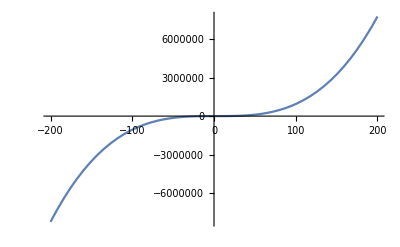

```mathematica
Plot[f[x], {x, -200, 200}]
```

```mathematica
f[x_] := Sin[Sqrt[x]] - x
```

```mathematica
f[4]
AnotherBisection[f_, a_, b_, err_, value_]:= Module[{aa, bb},
aa = N[a];
bb = N[b];
current_a = Abs[(value - f[aa]) / value] * 100;
If [current_a < err, Return[aa, Module]];
current_b = Abs[(value - f[bb]) / value] * 10;
If [current_b < err, Return[bb, Module]];
If [N[f[aa]]  N[f[(aa+bb)]] > 0, 
Return[AnotherBisection[f,(aa+bb)/2, bb,err, value], Module],
Return[AnotherBisection[f,aa,(aa+bb)/2, err, value]],Module]
]
```

-4+Sin[2]

```mathematica
g[x_] :=Sin[Sqrt[x]];
x0 = 0.5;

erra[x_, x1_] := Abs[(x1 - x)/ x1 ] * 100
err = erra[x0, g[x0]]
```

23.0339

```mathematica
erra[1,2]
a = []
a = [a, 12]
a
```

erra[1,2]

```mathematica
50
a
g[x0]
```

50

a

0.649637

```mathematica
0.+1.1722838862447986 ⅈ
```

0.+1.17228 ⅈ

```mathematica
err
```

23.0339

```mathematica
err < 0.1
errors = {}
```

False

{}

```mathematica
errors = Append[errors, 1]
```

```mathematica
{1.4705943773341136*^-9,1}
errors = Append[errors, 1]
```

{1.47059×10^-9,1}

{1.47059×10^-9,1,1}

```mathematica
errors = {}
err0  = 100
err = 100
err
```

{}

100

100

100

```mathematica
While[err > 0.000000001,
  err = erra[x0, g[x0]];
  AppendTo[errors, err / err0];
  err0 = err;
  x0 = g[x0];
]
```

```mathematica
errors
err0
err
```

{0.230339,0.432544,0.392673,0.3755,0.368785,0.366269,0.365341,0.365002,0.364878,0.364833,0.364816,0.36481,0.364808,0.364807,0.364807,0.364807,0.364807,0.364807,0.364807,0.364807,0.364807,0.364807,0.364806,0.364806,0.364809}

9.50187×10^-10

9.50187×10^-10

```mathematica
{0.2303393327540153,1.,0.43254444416765436,0.3926732177092647,0.37550036810597875,0.36878510443962487,0.3662686526955527,0.3653413870801824,0.36500186469409623,0.36487783742432267,0.3648325691544954,0.3648160520219841,0.36481002605795243,0.3648078277044279,0.3648070257778673,0.3648067330641601,0.36480662634429895,0.364806588278826,0.3648065721279866,0.36480656630373937,0.36480657838886904,0.364806510138646,0.3648067397761313,0.3648063823088788,0.36480622443715005,0.36480948498768856,0.36479440601834484,0.3648220685052474,0.3648201027982326,0.36474639949899945,0.3648068669527673,0.36470588235293305,0.36774193548386785}
```

{0.230339,1.,0.432544,0.392673,0.3755,0.368785,0.366269,0.365341,0.365002,0.364878,0.364833,0.364816,0.36481,0.364808,0.364807,0.364807,0.364807,0.364807,0.364807,0.364807,0.364807,0.364807,0.364807,0.364806,0.364806,0.364809,0.364794,0.364822,0.36482,0.364746,0.364807,0.364706,0.367742}

```mathematica
ListPlot[errors]
```

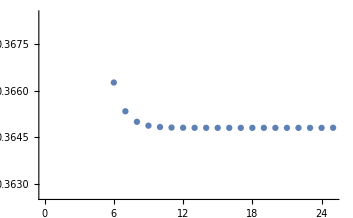
```mathematica
-Graphics-
f[x_]:= x^3 - 6 * x ^2 + 11x - 6.1;
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[errors]

```mathematica
xi = 0.5;
xiii = {};
For [i=0, i< 100,i=i+1,
     xii = xi -( f'[xi] / f[xi]);
     err = Abs[(xii-xi)/xii] * 100;
     xi = xii;
     AppendTo[xiii, xi];
]
```

5.75

```mathematica
xi
```

7.18079

```mathematica
err
```

109.524

```mathematica
for [i=0, i< 100,i++,
    Print[i];
]
```

1

for[0,True,0,Null]

```mathematica
For[i=0,i<4,i++,
Print[i];
]
```

0

1

2

3